```mathematica
Manipulate[Plot[{P*Sin[x]/x+Cos[x],1,-1},{x,0,10Pi}],{P,0,20}]
```

```mathematica
Manipulate[ContourPlot[{P*Sin[Sqrt[x]]/Sqrt[x]+Cos[Sqrt[x]]==Cos[k]},{k,0,2Pi},{x,0,15},ColorFunction->"Rainbow"],{P,0,20}]
```

```mathematica
firstroot[P_] :=FindRoot[P*Sin[x]/x+Cos[x]==1,{x,0.1,5}][[1,2]]
firstrootpi[P_] :=FindRoot[P*Sin[x]/x+Cos[x]==-1,{x,0.1,4}][[1,2]]
```

```mathematica
Energy0[P_]:=FindRoot[P*Sin[x]/x+Cos[x]==1,{x,0.1,100}][[1,2]]^2/2
MEFF[P_,K_]:=(P*(Sin[K]/K^2-Cos[K]/K)+Sin[K])/K
```

```mathematica
m0[P_]:=Module[{x,y},x=firstroot[P];MEFF[P,x]]
inversem0[P_]:=Module[{x,y},x=firstroot[P];1/MEFF[P,x]]
inversempi[P_]:=Module[{x,y},x=firstrootpi[P];-1/MEFF[P,x]]
```

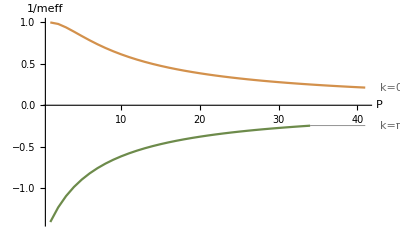

```mathematica
ListPlot[{Table[inversem0[p],{p,0,40,1}],Table[inversempi[p],{p,7,40,1}]},Joined->True,PlotRange->Full,AxesLabel->{"P","1/meff"},ColorFunction->"DarkRainbow",PlotLabels->{"k=0","k=π"}]
```